```mathematica
ψψ[η_,ξ_]=(η^2+ξ^2)^(1/4) Cos[1/2 Arg[η+I ξ]];
κκ[η_,ξ_]=(η^2+ξ^2)^(1/4) Sin[1/2 Arg[η+I ξ]];
```

ParametricPlot::exclul: {(Im[η] + Re[ξξ[η, 1, 10]]) - 0, Im[η^2 + ξξ[η, 1, 10]^2] - 0, (Im[η] + Re[ξξ[η, 1, 10]]) - 0, Im[η^2 + ξξ[η, 1, 10]^2] - 0} must be a list of equalities or real-valued functions.

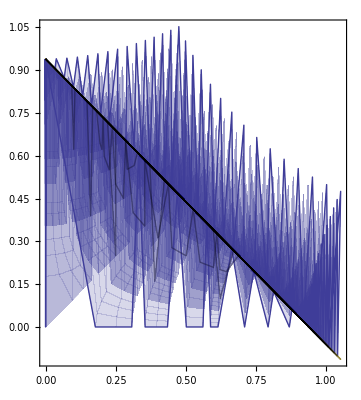

```mathematica
plotRp=10;
plota0=1;
plotr1=1;
plotr2=1;
plotη1=ArcSinh[plota0/plotr1];
plotη2=-ArcSinh[plota0/plotr2];

ParametricPlot[{{ψψ[η,ξ],κκ[η,ξ]},{ψψ[η,ξξ[η,plota0,plotRp]],κκ[η,ξξ[η,plota0,plotRp]]},{ψψ[η,ξ],-(√-plotη2)/(√plotη1)ψψ[η,ξ]+√-plotη2}},{ξ,0,1},{η,plotη2,plotη1}]
```

## Koordinatentransformation

```mathematica
Clear[s,ψ,m,κ]
Print["ψ:"]
s = A ψr[B] + (1-A)ψl[B] + (1/2)(1+B)ψu[A] + (1/2)(1-B)ψd[A] + α0 + α1 A + α2 B + α3 A B
sol1=(Solve[Coefficient[(s/.A->0) - ψl[B],B,0]==0,α0])[[1]][[1]]
sol2=(Solve[Coefficient[(s/.A->0) - ψl[B],B,1]==0,α2])[[1]][[1]]
sol3=(Solve[(Coefficient[(s/.A->1)- ψr[B],B,0]/.sol1/.sol2)==0,α1])[[1]][[1]]
sol4=(Solve[(Coefficient[(s/.A->1)- ψr[B],B,1]/.sol1/.sol2)==0,α3])[[1]][[1]]
ψ[A_,B_]=Simplify[s/.sol1/.sol2/.sol3/.sol4]
Clear[α0,α1,α2,α3,sol1,sol2,sol3,sol4];
Print["κ:"]
m = A κr[B] + (1-A)κl[B] + (1/2)(1+B)κu[A] + (1/2)(1-B)κd[A] + α0 + α1 A + α2 B + α3 A B
sol1=(Solve[Coefficient[(m/.A->0) - κl[B],B,0]==0,α0])[[1]][[1]]
sol2=(Solve[Coefficient[(m/.A->0) - κl[B],B,1]==0,α2])[[1]][[1]]
sol3=(Solve[(Coefficient[(m/.A->1)- κr[B],B,0]/.sol1/.sol2)==0,α1])[[1]][[1]]
sol4=(Solve[(Coefficient[(m/.A->1)- κr[B],B,1]/.sol1/.sol2)==0,α3])[[1]][[1]]
κ[A_,B_]=Simplify[m/.sol1/.sol2/.sol3/.sol4]
Clear[m,s];
```

```mathematica
α0+A α1+B α2+A B α3+1/2 (1-B) ψd[A]+(1-A) ψl[B]+A ψr[B]+1/2 (1+B) ψu[A]
```

```mathematica
α0->1/2 (-ψd[0]-ψu[0])
```

```mathematica
α2->1/2 (ψd[0]-ψu[0])
```

```mathematica
α1->1/2 (ψd[0]-ψd[1]+ψu[0]-ψu[1])
```

```mathematica
α3->1/2 (-ψd[0]+ψd[1]+ψu[0]-ψu[1])
```

```mathematica
1/2 (-ψd[0]+A ψd[0]+B ψd[0]-A B ψd[0]-A ψd[1]+A B ψd[1]-(-1+B) ψd[A]-2 (-1+A) ψl[B]+2 A ψr[B]-ψu[0]+A ψu[0]-B ψu[0]+A B ψu[0]-A ψu[1]-A B ψu[1]+ψu[A]+B ψu[A])
```

κ:

```mathematica
α0+A α1+B α2+A B α3+1/2 (1-B) κd[A]+(1-A) κl[B]+A κr[B]+1/2 (1+B) κu[A]
```

```mathematica
α0->1/2 (-κd[0]-κu[0])
```

```mathematica
α2->1/2 (κd[0]-κu[0])
```

```mathematica
α1->1/2 (κd[0]-κd[1]+κu[0]-κu[1])
```

```mathematica
α3->1/2 (-κd[0]+κd[1]+κu[0]-κu[1])
```

```mathematica
1/2 (-κd[0]+A κd[0]+B κd[0]-A B κd[0]-A κd[1]+A B κd[1]-(-1+B) κd[A]-2 (-1+A) κl[B]+2 A κr[B]-κu[0]+A κu[0]-B κu[0]+A B κu[0]-A κu[1]-A B κu[1]+κu[A]+B κu[A])
```

## Gebiet 2

```mathematica
Clear[ψl,ψr,ψd,ψu,ψ,κl,κr,κd,κu,κ]
ψ[A_,B_]=1/2 (-ψd[0]+A ψd[0]+B ψd[0]-A B ψd[0]-A ψd[1]+A B ψd[1]-(-1+B) ψd[A]-2 (-1+A) ψl[B]+2 A ψr[B]-ψu[0]+A ψu[0]-B ψu[0]+A B ψu[0]-A ψu[1]-A B ψu[1]+ψu[A]+B ψu[A]);
κ[A_,B_]=1/2 (-κd[0]+A κd[0]+B κd[0]-A B κd[0]-A κd[1]+A B κd[1]-(-1+B) κd[A]-2 (-1+A) κl[B]+2 A κr[B]-κu[0]+A κu[0]-B κu[0]+A B κu[0]-A κu[1]-A B κu[1]+κu[A]+B κu[A]);
ψr[B_]=ψψ[1/2 (-η1+η2)B + (η1+η2)/2,π];
κr[B_]=κκ[1/2 (-η1+η2)B + (η1+η2)/2,π];
ψu[A_]=ψψ[η2,A π];
κu[A_]=κκ[η2,A π];
ψl[B_]=-(√η1)/2 B +(√η1)/2;
κl [B_]=(√-η2)/2 B+(√-η2)/2;
ψd[A_]=ψψ[η1,A π];
κd[A_]=κκ[η1,A π];
(*ParametricPlot[{ψ[A,B],κ[A,B]},{A,0,1},{B,-1,1},PlotPoints->50]*)
(*Print["ψ=",Simplify[ψ[A,B],Assumptions:>η1>0&&η2<0]]
Print["κ=",Simplify[Simplify[κ[A,B],Assumptions:>η1>0&&η2<0]]]*)
```

```mathematica
replacearg={Arg[ⅈ π+η1]->atan2[π,η1],Arg[ⅈ π+η2]->atan2[π,η2],Arg[ⅈ A π+η2]->atan2[A π,η2],Arg[ⅈ A π+η1]->atan2[A π,η1],Arg[ⅈ π+1/2 B (-η1+η2)+(η1+η2)/2]->atan2[π,1/2 B (-η1+η2)+(η1+η2)/2], Arg[2 ⅈ π+η1-B η1+η2+B η2]->atan2[2π ,η1-B η1+η2+B η2]};
```

```mathematica
CForm[Simplify[κ[A,B],Assumptions:>a0>0&&Rp>0&&Rp>a0&&η1>0&&η2<0&&B≥-1&&B≤1&&A≥0&&A≤1]/.replacearg/.η1->eta1/.η2->eta2]/.Power->pow/.Sin->sin/.Cos->cos/.ArcCosh->acosh/.ArcCos->acos
```

(A*(-1 + B)*pow(pow(eta1,2) + pow(Pi,2),0.25)*sin(atan2(Pi,eta1)/2.) - 
     A*pow(pow(eta2,2) + pow(Pi,2),0.25)*sin(atan2(Pi,eta2)/2.) - 
     A*B*pow(pow(eta2,2) + pow(Pi,2),0.25)*sin(atan2(Pi,eta2)/2.) + 
     A*pow(2,0.5)*pow(pow(eta1 - B*eta1 + eta2 + B*eta2,2) + 
        4*pow(Pi,2),0.25)*sin(atan2(2*Pi,
         eta1 - B*eta1 + eta2 + B*eta2)/2.) + 
     pow(pow(eta1,2) + pow(A,2)*pow(Pi,2),0.25)*
      sin(atan2(A*Pi,eta1)/2.) - 
     B*pow(pow(eta1,2) + pow(A,2)*pow(Pi,2),0.25)*
      sin(atan2(A*Pi,eta1)/2.) + 
     pow(pow(eta2,2) + pow(A,2)*pow(Pi,2),0.25)*
      sin(atan2(A*Pi,eta2)/2.) + 
     B*pow(pow(eta2,2) + pow(A,2)*pow(Pi,2),0.25)*
      sin(atan2(A*Pi,eta2)/2.))/2.

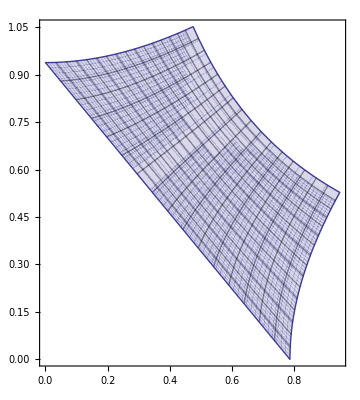

```mathematica
ParametricPlot[{ψ[A,B]/.a0->1/.Rp->7/.η1->0.62/.η2->-0.88,κ[A,B]/.a0->1/.Rp->7/.η1->0.62/.η2->-0.88},{A,0,1},{B,-1,1}]
```